## MODELAGEM DA DINÂMICA PLANA DE AERONAVE SUPERSÔNICA DE PASSAGEIROS DURANTE FASE DE FREE-ROLL DA ATERRISSAGEM

## PME3380 - Modelagem de Sistemas Dinâmicos Prof. Dr. Agenor de Toledo Fleury Prof. Dr. Renato Maia Matarazzo Orsino

## Grupo K Lucas Retore Carboni - 12676091 Roberto Tetsuo Hamaoka - 10334770 Vitor Lucas Buter - 12555700

## Modelo principal - toque e free-roll

O equacionamento é baseado no seguinte modelo físico:
-Graphics-

e  são definidos como variáveis incrementais a partir da posição de equilíbrio dinâmico do avião transladando em pista plana com velocidade constante (M.R.U)
Importando as funções necessárias ao código

```mathematica
SetDirectory @ NotebookDirectory[];
<<Linearize.m
```

As coordenadas generalizadas são definidas como:

```mathematica
𝕢[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t]};
𝕧[t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]}; 
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = { Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, 𝕧[t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
α = 𝕢[t][[3]] + Subscript[Φ, 0];
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, PO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor P-O*)
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, GO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor G-O*)
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
D[Subscript[H, o], t] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[𝕧[t][[1]], t]) + Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(𝕢[t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) - Subscript[L, ext][[2]]//FullSimplify;
```

### O espaço de estados

```mathematica
DIN = {Subscript[TMB, m], Subscript[TMB, M], TQMA};

Sol[t_] = Flatten @ Solve[
	(# == 0)& /@ DIN,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;

𝕩[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
F = (𝕩'[t] /.Sol[t]); 
F //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
-(M Cos[Φ_0+θ[t]] D_GO^2 (2 g M Cos[Φ_0+θ[t]]+Sin[Φ_0+θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol)+1/2 M D_GO (-S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2+4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2)+J_oz (S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(2 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(Sec[Φ_0+θ[t]] (-S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D Tan[Φ_0+θ[t]])+2 M Sin[Φ_0+θ[t]] D_GO^2 θ'[t]^2+D_GO (S ρ C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])+2 (g M-g M μ_rol Tan[Φ_0+θ[t]]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t])))))/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz))

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
POSequi = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINlin = Linearize[DIN, POSequi]; (*ELS -> Equação dinâmica não-linear*)

Sollin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINlin,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
	
Subscript[𝕩, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[F, lin] = (Subscript[𝕩, lin]'[t] /.Sollin[t]);
Subscript[F, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(2 M Cos[Φ_0] D_GO^2 ((2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])+2 g M (-Cos[Φ_0]+Sin[Φ_0] θ[t]))+2 M S ρ Cos[Φ_0] D_GO D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))-2 J_oz (S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(4 M (M Cos[Φ_0]^2 D_GO^2-J_oz))
(-S ρ D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))+D_GO (-2 g M Sin[Φ_0] (μ_rol+θ[t])+S ρ C_L (u_longit+u_vento)^2 (Cos[Φ_0]+μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t]))+2 Cos[Φ_0] (g M-g M μ_rol θ[t]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t]))))/(2 M Cos[Φ_0]^2 D_GO^2-2 J_oz))

```mathematica
rep = {Subscript[C, D] -> 0.00017*Subscript[Φ, 0]^2 + 0.01111*Subscript[Φ, 0] + 0.15714, Subscript[C, L] -> -0.00165*Subscript[Φ, 0]^2 + 0.07378*Subscript[Φ, 0] + 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, m -> 3000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, ρ -> 1.2923, S -> ((25.66/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
𝔸 = CoefficientArrays[Subscript[F, lin], Subscript[𝕩, lin][t]][[2]]//Normal; 
𝔸 //FullSimplify//MatrixForm;

𝔹 = CoefficientArrays[Subscript[F, lin], 𝕦[t]][[2]]//Normal; 
𝔹 //MatrixForm;

ℂ = { {0,1,0,0,0,0}, {0,0,1,0,0,0}, {0,0,0,0,1,0}, {0,0,0,0,0,1}};
ℂ //MatrixForm;

𝔻 = {{0,0},{0,0},{0,0},{0,0}};
𝔻 //MatrixForm;

𝕩[t] //MatrixForm ;
𝕩'[t] //MatrixForm;
𝕦[t] //MatrixForm;
𝕪[t] //MatrixForm ;
𝔸.𝕩[t] //MatrixForm;

Polos = 𝔸/.(rep)/.(Subscript[Φ, 0]->a)/.(Subscript[u, vento]->v)/.(Subscript[C, pav]->1)/.(Subscript[u, longit]->u);
Polos //MatrixForm;
```

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.00017*Subscript[Φ, 0]^2 + 0.01111*Subscript[Φ, 0] + 0.15714, Subscript[C, L] -> -0.00165*Subscript[Φ, 0]^2 + 0.07378*Subscript[Φ, 0] + 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, m -> 3000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, ρ -> 1.2923, S -> ((25.66/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸/.(rep)/.(Subscript[Φ, 0]->13*Pi/180)/.(Subscript[u, longit]->280/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹/.(rep)/.(Subscript[Φ, 0]->13*Pi/180)/.(Subscript[u, longit]->280/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂ, 𝔻}]
```

000100000000100000000100-125434/1557434/150-13987/37525549/750013600/397/30133.739-133.739-0.08243611.18985-1.18985000-1.495941.495940.0384566-0.01330910.013309100001000000001000000000100000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2461FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TF = TransferFunctionModel[SS, s]
```

```mathematica
(606281.3773692653+5393.976707318789 s)/(606273.6665483696+5826.363590991822 s+8499.85145826268 s^2+38.48851446975169 s^3+s^4)(432.42127650592005+3.8471745633087266 s)/(606273.6665483698+5826.363590991825 s+8499.85145826268 s^2+38.48851446975169 s^3+s^4)-(60.334684545357966 (-9.64746254199912*^-13-2.6850847895212396*^-14 s+112.3997025323875 s^2+s^3))/(-22756.462609476046-218.69087987190622 s+605954.6289428258 s^2+5824.918944157974 s^3+8499.813923770798 s^4+38.48851446975169 s^5+s^6)-(0.0430328264765194 (112.39970253680417 s^2+s^3))/(-22756.462609476046-218.69087987190622 s+605954.6289428258 s^2+5824.918944157974 s^3+8499.813923770798 s^4+38.48851446975169 s^5+s^6)(606281.3773692654 s+5393.976707318787 s^2)/(606273.670594448+5826.36360931295 s+8499.851458738694 s^2+38.48851446975169 s^3+s^4)(432.4212765060202 s+3.847174563306908 s^2)/(606273.6705944478+5826.363609312949 s+8499.851458738694 s^2+38.48851446975169 s^3+s^4)(-6781.600595283669 s^3-60.334684545357966 s^4)/(-22756.462609476046-218.69087987190622 s+605954.6289428258 s^2+5824.918944157974 s^3+8499.813923770798 s^4+38.48851446975169 s^5+s^6)(-4.836876895165915 s^3-0.0430328264774289 s^4)/(-22756.462609476046-218.69087987190622 s+605954.6289428258 s^2+5824.918944157974 s^3+8499.813923770798 s^4+38.48851446975169 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606281.3773692653432.42127650592005-60.334684545357966-0.0430328264765194606281.3773692654432.4212765060202-6781.600595283669-4.836876895165915606273.6665483696606273.6665483698-22756.462609476046-22756.462609476046606273.670594448606273.6705944478-22756.462609476046-22756.4626094760461FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
TransferFunctionPoles[TF] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TF] [[4]][[1]] //MatrixForm
```

(-19.0613-89.7246 ⅈ
-19.0613+89.7246 ⅈ
-0.182995-8.48665 ⅈ
-0.182995+8.48665 ⅈ)

(-19.0613-89.7246 ⅈ
-19.0613+89.7246 ⅈ
-0.193739
-0.182995-8.48665 ⅈ
-0.182995+8.48665 ⅈ
0.193739)

```mathematica
TransferFunctionZeros[TF]
```

{{{-112.4},{-112.4}},{{-112.4,-9.26454×10^-8,9.26454×10^-8},{-112.4,0,0}},{{-112.4,0},{-112.4,0}},{{-112.4,0,0,0},{-112.4,0,0,0}}}

### Decomposição em frações parciais

((72.7837+0.317715 s)/(72.0567+0.36599 s+1. s^2)+(-84.7795-0.317715 s)/(8413.84+38.1225 s+1. s^2) | (0.0519119+0.000226605 s)/(72.0567+0.36599 s+1. s^2)+(-0.0604677-0.000226605 s)/(8413.84+38.1225 s+1. s^2)
-0.00108284/(-0.193739+1. s)+0.00108314/(0.193739+1. s)+(-0.813703-0.00355412 s)/(72.0567+0.36599 s+1. s^2)+(0.948302+0.00355382 s)/(8413.84+38.1225 s+1. s^2) | -(7.72318×10^-7)/(-0.193739+1. s)+(7.72531×10^-7)/(0.193739+1. s)+(-0.000580362-2.53492×10^-6 s)/(72.0567+0.36599 s+1. s^2)+(0.000676363+2.53471×10^-6 s)/(8413.84+38.1225 s+1. s^2)
(-22.8935+72.6674 s)/(72.0567+0.36599 s+1. s^2)+(2673.2-72.6674 s)/(8413.84+38.1225 s+1. s^2) | (-0.0163284+0.0518289 s)/(72.0567+0.36599 s+1. s^2)+(1.90662-0.0518289 s)/(8413.84+38.1225 s+1. s^2)
-0.000209788/(-0.193739+1. s)-0.000209846/(0.193739+1. s)+(0.256098-0.812402 s)/(72.0567+0.36599 s+1. s^2)+(-29.9013+0.812822 s)/(8413.84+38.1225 s+1. s^2) | -(1.49628×10^-7)/(-0.193739+1. s)-(1.4967×10^-7)/(0.193739+1. s)+(0.000182658-0.000579434 s)/(72.0567+0.36599 s+1. s^2)+(-0.0213267+0.000579733 s)/(8413.84+38.1225 s+1. s^2))

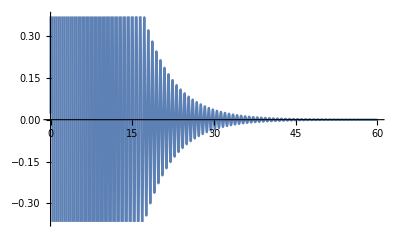

```mathematica
FP = Apart[TF[s]]; 
OutputResponse[{SS,{0,0,0,-3,-3,0}}, 0, t] [[2]][[2]]//ComplexExpand //MatrixForm;
FP//MatrixForm
IL = InverseLaplaceTransform[FP,s, t] //ComplexExpand;
Plot[IL[[1]][[1]], {t, 0, 60}]
(*https://lpsa.swarthmore.edu/Transient/TransMethTF.html#:~:text=To%20find%20the%20complete%20response,the%20zero%20input%20differential%20equation.*)
```

### Diagrama de Bode

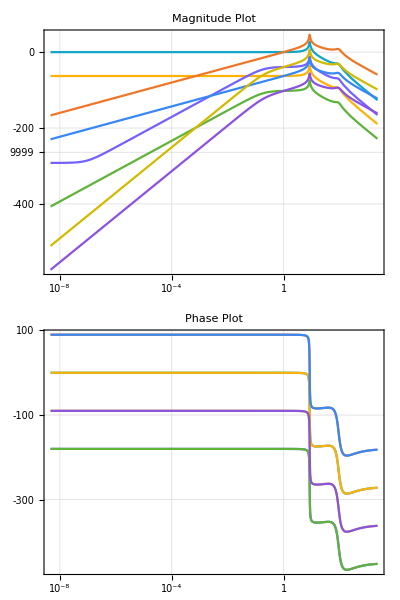

```mathematica
BodePlot[TF, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Pós toque

### Modelo incluindo trem de pouso frontal

-Graphics-

```mathematica
Subscript[𝕢, T][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t]};
Subscript[𝕧, T][t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = {Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, Subscript[𝕧, T][t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, PO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor P-O*);
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, GO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor G-O*);
Subscript[ρ, FO] = {Subscript[D, FO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, FO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor G-O*);
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[F, f] = {0, -Subscript[k, Tf]*(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]), t]), 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, Tf] = Cross[Subscript[ρ, FO], Subscript[F, f]] //FullSimplify;
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso] - Subscript[M, Tf])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m e mf) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[Subscript[𝕧, T][t][[1]], t]) + Subscript[k, r]*(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]) - Subscript[c, t]*(D[(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]), t]) //FullSimplify;
Subscript[TMB, mf] = Subscript[m, f]*(D[Subscript[𝕧, T][t][[4]], t]) + Subscript[k, rf]*(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]) + Subscript[c, rf]*(D[(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]), t]) - Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) + Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) - Subscript[L, ext][[2]] //FullSimplify;
noequi =  Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) //FullSimplify;
```

### O espaço de estados

```mathematica
DINf = {Subscript[TMB, m], Subscript[TMB, M], TQMA, Subscript[TMB, mf]};

Solf[t_] = Flatten @ Solve[
	(# == 0)& /@ DINf,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
𝕩f[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Ff = (𝕩f'[t] /.Solf[t]); 
Ff //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-4 g M Cos[Φ_0+θ[t]]^2+Sin[2 (Φ_0+θ[t])] (2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol)+M D_GO (S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2-4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2-4 Cos[Φ_0+θ[t]]^2 D_FO^2 (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+4 Cos[Φ_0+θ[t]]^2 D_FO (k_Tf (-q_2[t]+q_3[t])+c_Tf (-q_2'[t]+q_3'[t])))+2 J_oz (-S ρ C_L (u_longit+u_vento)^2+2 D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])-2 (k_t (q_1[t]-q_2[t])+k_Tf (-q_2[t]+q_3[t])+c_t (q_1'[t]-q_2'[t])+c_Tf (-q_2'[t]+q_3'[t]))))/(4 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(-S ρ Sec[Φ_0+θ[t]] C_L D_PO (u_longit+u_vento)^2+2 D_FO^2 k_Tf Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit^2 Tan[Φ_0+θ[t]]-2 S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit u_vento Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_vento^2 Tan[Φ_0+θ[t]]+2 Sec[Φ_0+θ[t]] D_FO k_Tf q_2[t]-2 Sec[Φ_0+θ[t]] D_FO k_Tf q_3[t]+2 c_Tf D_FO^2 θ'[t]+2 M D_GO^2 Tan[Φ_0+θ[t]] θ'[t]^2+2 Sec[Φ_0+θ[t]] c_Tf D_FO q_2'[t]+D_GO (S ρ Sec[Φ_0+θ[t]] C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])-2 (D_FO (k_Tf Tan[Φ_0+θ[t]]+c_Tf θ'[t])+Sec[Φ_0+θ[t]] (-g M+g M μ_rol Tan[Φ_0+θ[t]]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))-2 Sec[Φ_0+θ[t]] c_Tf D_FO q_3'[t])/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
POSequif = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> - Subscript[Φ, 0], Subscript[q, 3][t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINflin = Linearize[DINf, POSequif]; (*ELS -> Equação dinâmica não-linear*)

Solflin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINflin,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
Subscript[𝕩f, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Subscript[Ff, lin] = (Subscript[𝕩f, lin]'[t] /.Solflin[t]);
Subscript[Ff, lin] //TrigReduce //FullSimplify //MatrixForm 
(*aquiiiiiiiiiiiiiiiiiiiiiiiii*)
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-2 g M+(2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol θ[t])+M D_GO (S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ[t])-2 D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])))-J_oz (S ρ C_L (u_longit+u_vento)^2-2 (k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))/(2 M (M D_GO^2-J_oz))
(-S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ[t])+D_GO (S ρ C_L (u_longit+u_vento)^2 (1+μ_rol θ[t])-2 (-g M+g M μ_rol θ[t]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t])))+2 D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])))/(2 M D_GO^2-2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

```mathematica
𝔸f = CoefficientArrays[Subscript[Ff, lin], Subscript[𝕩f, lin][t]][[2]]//Normal; 
𝔸f //FullSimplify//MatrixForm;

𝔹f = CoefficientArrays[Subscript[Ff, lin], 𝕦[t]][[2]]//Normal; 
𝔹f //MatrixForm;

ℂf = { {0,1,0,0,0,0,0,0}, {0,0,1,0,0,0,0,0}, {0,0,0,0,0,1,0,0}, {0,0,0,0,0,0,1,0}};
ℂf //MatrixForm;

𝔻f = {{0,0},{0,0},{0,0},{0,0}};
𝔻f //MatrixForm;
 
𝕩f[t] //MatrixForm ;
𝕩f'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
```

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.15714, Subscript[C, L] -> 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, Subscript[k, Tf] -> 5743400, Subscript[c, Tf] -> 51098, Subscript[k, rf]-> 3400000, Subscript[c, rf] -> 2425, m -> 3000, Subscript[m, f] -> 1500, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, Subscript[D, FO] -> 32.5, ρ -> 1.2923, S -> ((25.6/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂf, 𝔻f}]
```

0000100000000001000000000010000000000100-125434/1557434/1500-13987/37525549/7500013600/397/30133.914-175.89-1364.2641.97581.19141-1.56486-12.13720.37345100-1.5373-9.04913-344.03910.5864-0.0136771-0.0805085-3.061030.094185600057434/15124440.-30478/5025549/7501107.12-17841/5006800/397/600100000000001000000000000100000000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2481FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TFf = TransferFunctionModel[SS, s]
```

(6247.54 (7.92141×10^7+1.46607×10^6 s+761891. s^2+11064.4 s^3+151.067 s^4+s^5))/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)(4.45596 (7.92141×10^7+1.46607×10^6 s+761891. s^2+11064.4 s^3+151.067 s^4+s^5))/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)(0.000366211+5.72205×10^-6 s+1.5482×10^8 s^2+1.99386×10^6 s^3+22511.3 s^4+151.484 s^5)/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)(0.000488281+3.8147×10^-6 s+110423. s^2+1422.09 s^3+16.0558 s^4+0.108044 s^5)/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)(4.94893×10^11 s+9.15932×10^9 s^2+4.75994×10^9 s^3+6.91252×10^7 s^4+943800. s^5+6247.54 s^6)/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)(3.52975×10^8 s+6.53275×10^6 s^2+3.39496×10^6 s^3+49302.5 s^4+673.151 s^5+4.45596 s^6)/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)(0.0000114441 s+1.90735×10^-6 s^2+1.5482×10^8 s^3+1.99386×10^6 s^4+22511.3 s^5+151.484 s^6)/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)(7.62939×10^-6 s+1.90735×10^-6 s^2+110423. s^3+1422.09 s^4+16.0558 s^5+0.108044 s^6)/(4.94893×10^11+9.51229×10^9 s+1.13961×10^10 s^2+1.6629×10^8 s^3+5.71692×10^7 s^4+596361. s^5+16492.5 s^6+77.6066 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s246247.5373281163634.4559641237137840.00036621093750.000488281254.948928492582754e113.529750468974476e80.0000114440917968757.62939453125e-64.9489284925827515e114.9489284925827515e114.9489284925827515e114.9489284925827515e114.9489284925827515e114.9489284925827515e114.9489284925827515e114.9489284925827515e111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[TFf] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TFf] [[4]][[1]] //MatrixForm
```

(-19.3127-77.1853 ⅈ
-19.3127+77.1853 ⅈ
-19.0664-89.7226 ⅈ
-19.0664+89.7226 ⅈ
-0.267914-12.1146 ⅈ
-0.267914+12.1146 ⅈ
-0.156236-7.95323 ⅈ
-0.156236+7.95323 ⅈ)

(-19.3127-77.1853 ⅈ
-19.3127+77.1853 ⅈ
-19.0664-89.7226 ⅈ
-19.0664+89.7226 ⅈ
-0.267914-12.1146 ⅈ
-0.267914+12.1146 ⅈ
-0.156236-7.95323 ⅈ
-0.156236+7.95323 ⅈ)

```mathematica
TransferFunctionZeros[TFf]
```

{{{-112.4,-19.1303-78.9288 ⅈ,-19.1303+78.9288 ⅈ,-0.20355-10.3348 ⅈ,-0.20355+10.3348 ⅈ},{-112.4,-19.1303-78.9288 ⅈ,-19.1303+78.9288 ⅈ,-0.20355-10.3348 ⅈ,-0.20355+10.3348 ⅈ}},{{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,-3.2482×10^-15-1.53799×10^-6 ⅈ,-3.2482×10^-15+1.53799×10^-6 ⅈ},{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,1.12009×10^-11-0.0000664975 ⅈ,1.12009×10^-11+0.0000664975 ⅈ}},{{-112.4,-19.1303-78.9288 ⅈ,-19.1303+78.9288 ⅈ,-0.20355-10.3348 ⅈ,-0.20355+10.3348 ⅈ,0},{-112.4,-19.1303-78.9288 ⅈ,-19.1303+78.9288 ⅈ,-0.20355-10.3348 ⅈ,-0.20355+10.3348 ⅈ,0}},{{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,-5.68392×10^-15-2.7188×10^-7 ⅈ,-5.68392×10^-15+2.7188×10^-7 ⅈ,0},{-112.4,-18.1024-93.6216 ⅈ,-18.1024+93.6216 ⅈ,-8.19166×10^-12-8.31219×10^-6 ⅈ,-8.19166×10^-12+8.31219×10^-6 ⅈ,0}}}

### Diagrama de Bode

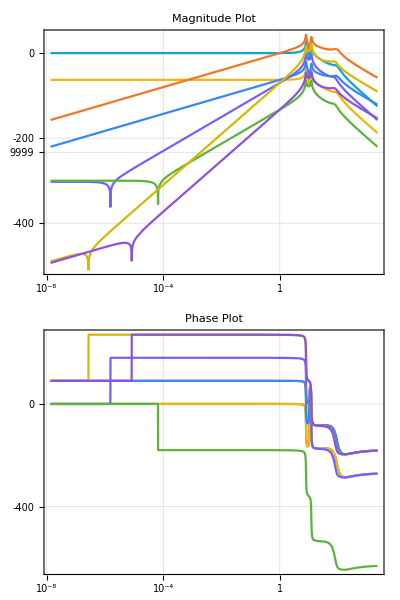

```mathematica
BodePlot[TFf, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Exportando o aquivo .m do espaço de estados

Para exportar outro espaço de estados, basta substituir o argumento da 4 linha da terceira célula de código por:
WriteString[fileD, (#/.(({ii_}→vv_):>(StringReplace[StringReplace[ToString @ StringForm[“    ``;”, (vv /. crule //CForm)], csqrule], csorule]<>”\n”)))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩’[t]/.NOMEDASOLUCAO[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};
```

```mathematica
fileD = OpenWrite["trab_esp_linearizado0.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(Subscript[𝕩f, lin]'[t]/.Solflin[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));
WriteString[fileD, "\n"];
Close[fileD];
```